```mathematica
ClearAll["Global`*"]
```

```mathematica
E0=1;
e=1;
c=1;
γ=1;
ω=1;
k=1;
x=1;
y[t_]:=-(E0 e c)/(γ ω^2)Cos[ω t-k x]
x[t_]:=-c/(8ω) ((e E0)/(γ ω))^2 Sin[2(ω t-k x)]
ParametricPlot[{x[t],y[t]},{t,0,10}]
```

SetDelayed::write: Tag Integer in 1[t_] is Protected.

$Failed

-Graphics-

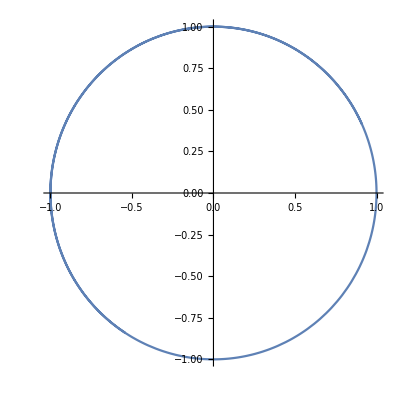

```mathematica
ParametricPlot[{-(E0 e c)/(γ ω^2)Cos[ω t-k x],(E0 e c)/(γ ω^2)Sin[ω t-k x]},{t,0,10}]
```

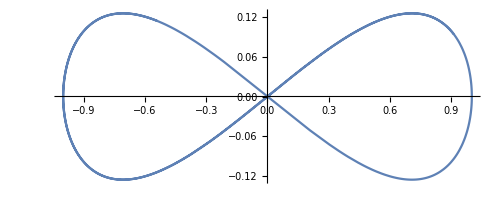

```mathematica
ParametricPlot[{-(E0 e c)/(γ ω^2)Cos[ω t-k x],-c/(8ω) ((e E0)/(γ ω))^2 Sin[2(ω t-k x)]},{t,0,10}]
```

```mathematica
(ϰy*ξ)/γ-e/(c*γ)Integrate[Ay,ξ]
```

```mathematica
(ϰz*ξ)/γ-e/(c*γ)Integrate[Az,ξ]
```

```mathematica
1/2((m^2*c^2+ϰ^2)/γ^2-1)ξ-e/(c*γ^2)Integrate[ϰ.A,ξ]+e^2/(2 γ^2*c^2)Integrate[A^2,ξ]
```

```mathematica
i[t_]:=(2 e^4)/(3 m^2 c^3)((Evec+1/c*Cross[v,H])^2-1/c^2*(Evec.v)^2)/(1-v^2/c^2)
```

```mathematica
S[ω_]:=Integrate[Exp[I*ω*t]*i[t],{t,0,∞}]
```